```mathematica
m=1;
ω=1;
ℏ=UnitConvert[Quantity[1,"PlanckConstant"],"SIBase"];
ℏ=QuantityMagnitude[ℏ];
ℏ=1;
Energy[n_]:=(2 n+1) ℏ/2 ω;

ψ[z_,n_]:=1/2 1/Sqrt[2^n n!] ((m ω)/(π ℏ))^(1/4) Exp[-((m ω z^2)/(2 ℏ))] HermiteH[n,Sqrt[(m ω)/ℏ] z];
```

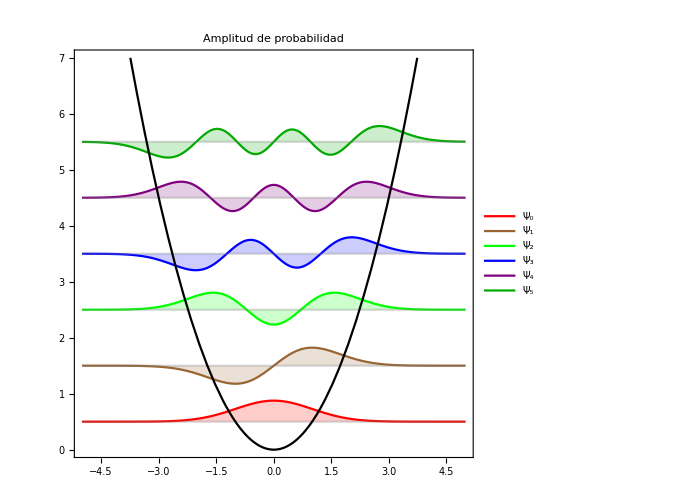

```mathematica
Plot[{Evaluate@Table[Energy[n]+ψ[z,n],{n,0,5}],Evaluate@Table[Energy[n],{n,0,5}],z^2/2},{z,-5,5},PlotRange->{0,7},PlotStyle->Join[{Red,Brown,Green,Blue,Purple,Darker[Green]},Table[{Gray,Opacity[0.3]},{n,0,5}],{Black}],Filling->{1->Energy[0],2->Energy[1], 3->Energy[2],4->Energy[3], 5->Energy[4], 6->Energy[5]}, PlotLabel->Style["Amplitud de probabilidad", FontSize->18, Black],PlotLegends->{"Ψ_0","Ψ_1","Ψ_2","Ψ_3","Ψ_4","Ψ_5" },Frame->True,AspectRatio->1,ImageSize->500]
```

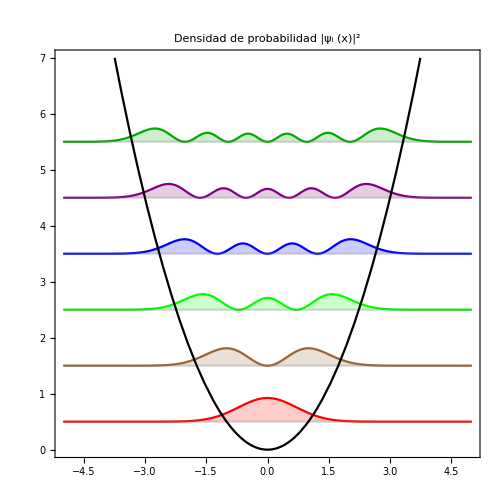

```mathematica
Plot[{Evaluate@Table[Energy[n]+3ψ[z,n]^2,{n,0,5}],Evaluate@Table[Energy[n],{n,0,5}],z^2/2},{z,-5,5},PlotRange->{0,7},PlotStyle->Join[{Red,Brown,Green,Blue,Purple,Darker[Green]},Table[{Gray,Opacity[0.3]},{n,0,5}],{Black}],Filling->{1->Energy[0],2->Energy[1], 3->Energy[2],4->Energy[3], 5->Energy[4], 6->Energy[5]}, PlotLabel->Style["Densidad de probabilidad |ψ_i (x)|^2", FontSize->18, Black],Frame->True,AspectRatio->1,ImageSize->500]
```